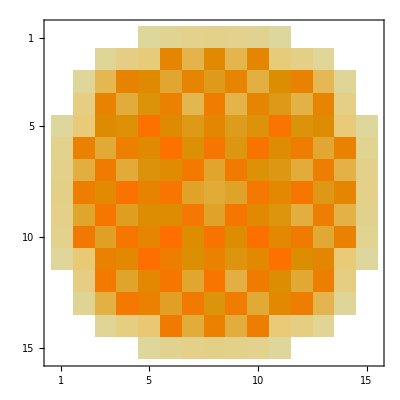

```mathematica
Clear["Global`*"];
(* Read in the plant ASCII data for a 193 fuel assembly reactor and plot some slices in 2D and 3D of the power distribution *) 
SetDirectory["C:\\Users\\public\\"];
data01=Import["dat_20110701_030516_s power.tmp","CSV"];

(* read in the 2D segment data from the power plant's ASCII files *)
GetSegmentData[datas_,seg_]:=Module[{tabs=Table[0.0,{i,1,15},{j,1,15}],len=Length[datas]},For[h=0,h<len,h++,tibs=datas[[h+1]][[1]];tubs=datas[[h+1]][[seg+1]];

If[Length[StringPosition[tibs,"_5 A"]]>0,tabs[[15]][[5]]=tubs;];
If[Length[StringPosition[tibs,"_6 A"]]>0,tabs[[15]][[6]]=tubs;];
If[Length[StringPosition[tibs,"_7 A"]]>0,tabs[[15]][[7]]=tubs;];
If[Length[StringPosition[tibs,"_8 A"]]>0,tabs[[15]][[8]]=tubs;];
If[Length[StringPosition[tibs,"_9 A"]]>0,tabs[[15]][[9]]=tubs;];
If[Length[StringPosition[tibs,"_10A"]]>0,tabs[[15]][[10]]=tubs;];
If[Length[StringPosition[tibs,"_11A"]]>0,tabs[[15]][[11]]=tubs;];

If[Length[StringPosition[tibs,"_3 B"]]>0,tabs[[14]][[3]]=tubs;];
If[Length[StringPosition[tibs,"_4 B"]]>0,tabs[[14]][[4]]=tubs;];
If[Length[StringPosition[tibs,"_5 B"]]>0,tabs[[14]][[5]]=tubs;];
If[Length[StringPosition[tibs,"_6 B"]]>0,tabs[[14]][[6]]=tubs;];
If[Length[StringPosition[tibs,"_7 B"]]>0,tabs[[14]][[7]]=tubs;];
If[Length[StringPosition[tibs,"_8 B"]]>0,tabs[[14]][[8]]=tubs;];
If[Length[StringPosition[tibs,"_9 B"]]>0,tabs[[14]][[9]]=tubs;];
If[Length[StringPosition[tibs,"_10B"]]>0,tabs[[14]][[10]]=tubs;];
If[Length[StringPosition[tibs,"_11B"]]>0,tabs[[14]][[11]]=tubs;];
If[Length[StringPosition[tibs,"_12B"]]>0,tabs[[14]][[12]]=tubs;];
If[Length[StringPosition[tibs,"_13B"]]>0,tabs[[14]][[13]]=tubs;];

If[Length[StringPosition[tibs,"_2 C"]]>0,tabs[[13]][[2]]=tubs;];
If[Length[StringPosition[tibs,"_3 C"]]>0,tabs[[13]][[3]]=tubs;];
If[Length[StringPosition[tibs,"_4 C"]]>0,tabs[[13]][[4]]=tubs;];
If[Length[StringPosition[tibs,"_5 C"]]>0,tabs[[13]][[5]]=tubs;];
If[Length[StringPosition[tibs,"_6 C"]]>0,tabs[[13]][[6]]=tubs;];
If[Length[StringPosition[tibs,"_7 C"]]>0,tabs[[13]][[7]]=tubs;];
If[Length[StringPosition[tibs,"_8 C"]]>0,tabs[[13]][[8]]=tubs;];
If[Length[StringPosition[tibs,"_9 C"]]>0,tabs[[13]][[9]]=tubs;];
If[Length[StringPosition[tibs,"_10C"]]>0,tabs[[13]][[10]]=tubs;];
If[Length[StringPosition[tibs,"_11C"]]>0,tabs[[13]][[11]]=tubs;];
If[Length[StringPosition[tibs,"_12C"]]>0,tabs[[13]][[12]]=tubs;];
If[Length[StringPosition[tibs,"_13C"]]>0,tabs[[13]][[13]]=tubs;];
If[Length[StringPosition[tibs,"_14C"]]>0,tabs[[13]][[14]]=tubs;];

If[Length[StringPosition[tibs,"_2 D"]]>0,tabs[[12]][[2]]=tubs;];
If[Length[StringPosition[tibs,"_3 D"]]>0,tabs[[12]][[3]]=tubs;];
If[Length[StringPosition[tibs,"_4 D"]]>0,tabs[[12]][[4]]=tubs;];
If[Length[StringPosition[tibs,"_5 D"]]>0,tabs[[12]][[5]]=tubs;];
If[Length[StringPosition[tibs,"_6 D"]]>0,tabs[[12]][[6]]=tubs;];
If[Length[StringPosition[tibs,"_7 D"]]>0,tabs[[12]][[7]]=tubs;];
If[Length[StringPosition[tibs,"_8 D"]]>0,tabs[[12]][[8]]=tubs;];
If[Length[StringPosition[tibs,"_9 D"]]>0,tabs[[12]][[9]]=tubs;];
If[Length[StringPosition[tibs,"_10D"]]>0,tabs[[12]][[10]]=tubs;];
If[Length[StringPosition[tibs,"_11D"]]>0,tabs[[12]][[11]]=tubs;];
If[Length[StringPosition[tibs,"_12D"]]>0,tabs[[12]][[12]]=tubs;];
If[Length[StringPosition[tibs,"_13D"]]>0,tabs[[12]][[13]]=tubs;];
If[Length[StringPosition[tibs,"_14D"]]>0,tabs[[12]][[14]]=tubs;];

If[Length[StringPosition[tibs,"_1 E"]]>0,tabs[[11]][[1]]=tubs;];
If[Length[StringPosition[tibs,"_2 E"]]>0,tabs[[11]][[2]]=tubs;];
If[Length[StringPosition[tibs,"_3 E"]]>0,tabs[[11]][[3]]=tubs;];
If[Length[StringPosition[tibs,"_4 E"]]>0,tabs[[11]][[4]]=tubs;];
If[Length[StringPosition[tibs,"_5 E"]]>0,tabs[[11]][[5]]=tubs;];
If[Length[StringPosition[tibs,"_6 E"]]>0,tabs[[11]][[6]]=tubs;];
If[Length[StringPosition[tibs,"_7 E"]]>0,tabs[[11]][[7]]=tubs;];
If[Length[StringPosition[tibs,"_8 E"]]>0,tabs[[11]][[8]]=tubs;];
If[Length[StringPosition[tibs,"_9 E"]]>0,tabs[[11]][[9]]=tubs;];
If[Length[StringPosition[tibs,"_10E"]]>0,tabs[[11]][[10]]=tubs;];
If[Length[StringPosition[tibs,"_11E"]]>0,tabs[[11]][[11]]=tubs;];
If[Length[StringPosition[tibs,"_12E"]]>0,tabs[[11]][[12]]=tubs;];
If[Length[StringPosition[tibs,"_13E"]]>0,tabs[[11]][[13]]=tubs;];
If[Length[StringPosition[tibs,"_14E"]]>0,tabs[[11]][[14]]=tubs;];
If[Length[StringPosition[tibs,"_15E"]]>0,tabs[[11]][[15]]=tubs;];

If[Length[StringPosition[tibs,"_1 F"]]>0,tabs[[10]][[1]]=tubs;];
If[Length[StringPosition[tibs,"_2 F"]]>0,tabs[[10]][[2]]=tubs;];
If[Length[StringPosition[tibs,"_3 F"]]>0,tabs[[10]][[3]]=tubs;];
If[Length[StringPosition[tibs,"_4 F"]]>0,tabs[[10]][[4]]=tubs;];
If[Length[StringPosition[tibs,"_5 F"]]>0,tabs[[10]][[5]]=tubs;];
If[Length[StringPosition[tibs,"_6 F"]]>0,tabs[[10]][[6]]=tubs;];
If[Length[StringPosition[tibs,"_7 F"]]>0,tabs[[10]][[7]]=tubs;];
If[Length[StringPosition[tibs,"_8 F"]]>0,tabs[[10]][[8]]=tubs;];
If[Length[StringPosition[tibs,"_9 F"]]>0,tabs[[10]][[9]]=tubs;];
If[Length[StringPosition[tibs,"_10F"]]>0,tabs[[10]][[10]]=tubs;];
If[Length[StringPosition[tibs,"_11F"]]>0,tabs[[10]][[11]]=tubs;];
If[Length[StringPosition[tibs,"_12F"]]>0,tabs[[10]][[12]]=tubs;];
If[Length[StringPosition[tibs,"_13F"]]>0,tabs[[10]][[13]]=tubs;];
If[Length[StringPosition[tibs,"_14F"]]>0,tabs[[10]][[14]]=tubs;];
If[Length[StringPosition[tibs,"_15F"]]>0,tabs[[10]][[15]]=tubs;];

If[Length[StringPosition[tibs,"_1 G"]]>0,tabs[[9]][[1]]=tubs;];
If[Length[StringPosition[tibs,"_2 G"]]>0,tabs[[9]][[2]]=tubs;];
If[Length[StringPosition[tibs,"_3 G"]]>0,tabs[[9]][[3]]=tubs;];
If[Length[StringPosition[tibs,"_4 G"]]>0,tabs[[9]][[4]]=tubs;];
If[Length[StringPosition[tibs,"_5 G"]]>0,tabs[[9]][[5]]=tubs;];
If[Length[StringPosition[tibs,"_6 G"]]>0,tabs[[9]][[6]]=tubs;];
If[Length[StringPosition[tibs,"_7 G"]]>0,tabs[[9]][[7]]=tubs;];
If[Length[StringPosition[tibs,"_8 G"]]>0,tabs[[9]][[8]]=tubs;];
If[Length[StringPosition[tibs,"_9 G"]]>0,tabs[[9]][[9]]=tubs;];
If[Length[StringPosition[tibs,"_10G"]]>0,tabs[[9]][[10]]=tubs;];
If[Length[StringPosition[tibs,"_11G"]]>0,tabs[[9]][[11]]=tubs;];
If[Length[StringPosition[tibs,"_12G"]]>0,tabs[[9]][[12]]=tubs;];
If[Length[StringPosition[tibs,"_13G"]]>0,tabs[[9]][[13]]=tubs;];
If[Length[StringPosition[tibs,"_14G"]]>0,tabs[[9]][[14]]=tubs;];
If[Length[StringPosition[tibs,"_15G"]]>0,tabs[[9]][[15]]=tubs;];

If[Length[StringPosition[tibs,"_1 H"]]>0,tabs[[8]][[1]]=tubs;];
If[Length[StringPosition[tibs,"_2 H"]]>0,tabs[[8]][[2]]=tubs;];
If[Length[StringPosition[tibs,"_3 H"]]>0,tabs[[8]][[3]]=tubs;];
If[Length[StringPosition[tibs,"_4 H"]]>0,tabs[[8]][[4]]=tubs;];
If[Length[StringPosition[tibs,"_5 H"]]>0,tabs[[8]][[5]]=tubs;];
If[Length[StringPosition[tibs,"_6 H"]]>0,tabs[[8]][[6]]=tubs;];
If[Length[StringPosition[tibs,"_7 H"]]>0,tabs[[8]][[7]]=tubs;];
If[Length[StringPosition[tibs,"_8 H"]]>0,tabs[[8]][[8]]=tubs;];
If[Length[StringPosition[tibs,"_9 H"]]>0,tabs[[8]][[9]]=tubs;];
If[Length[StringPosition[tibs,"_10H"]]>0,tabs[[8]][[10]]=tubs;];
If[Length[StringPosition[tibs,"_11H"]]>0,tabs[[8]][[11]]=tubs;];
If[Length[StringPosition[tibs,"_12H"]]>0,tabs[[8]][[12]]=tubs;];
If[Length[StringPosition[tibs,"_13H"]]>0,tabs[[8]][[13]]=tubs;];
If[Length[StringPosition[tibs,"_14H"]]>0,tabs[[8]][[14]]=tubs;];
If[Length[StringPosition[tibs,"_15H"]]>0,tabs[[8]][[15]]=tubs;];

If[Length[StringPosition[tibs,"_1 J"]]>0,tabs[[7]][[1]]=tubs;];
If[Length[StringPosition[tibs,"_2 J"]]>0,tabs[[7]][[2]]=tubs;];
If[Length[StringPosition[tibs,"_3 J"]]>0,tabs[[7]][[3]]=tubs;];
If[Length[StringPosition[tibs,"_4 J"]]>0,tabs[[7]][[4]]=tubs;];
If[Length[StringPosition[tibs,"_5 J"]]>0,tabs[[7]][[5]]=tubs;];
If[Length[StringPosition[tibs,"_6 J"]]>0,tabs[[7]][[6]]=tubs;];
If[Length[StringPosition[tibs,"_7 J"]]>0,tabs[[7]][[7]]=tubs;];
If[Length[StringPosition[tibs,"_8 J"]]>0,tabs[[7]][[8]]=tubs;];
If[Length[StringPosition[tibs,"_9 J"]]>0,tabs[[7]][[9]]=tubs;];
If[Length[StringPosition[tibs,"_10J"]]>0,tabs[[7]][[10]]=tubs;];
If[Length[StringPosition[tibs,"_11J"]]>0,tabs[[7]][[11]]=tubs;];
If[Length[StringPosition[tibs,"_12J"]]>0,tabs[[7]][[12]]=tubs;];
If[Length[StringPosition[tibs,"_13J"]]>0,tabs[[7]][[13]]=tubs;];
If[Length[StringPosition[tibs,"_14J"]]>0,tabs[[7]][[14]]=tubs;];
If[Length[StringPosition[tibs,"_15J"]]>0,tabs[[7]][[15]]=tubs;];

If[Length[StringPosition[tibs,"_1 K"]]>0,tabs[[6]][[1]]=tubs;];
If[Length[StringPosition[tibs,"_2 K"]]>0,tabs[[6]][[2]]=tubs;];
If[Length[StringPosition[tibs,"_3 K"]]>0,tabs[[6]][[3]]=tubs;];
If[Length[StringPosition[tibs,"_4 K"]]>0,tabs[[6]][[4]]=tubs;];
If[Length[StringPosition[tibs,"_5 K"]]>0,tabs[[6]][[5]]=tubs;];
If[Length[StringPosition[tibs,"_6 K"]]>0,tabs[[6]][[6]]=tubs;];
If[Length[StringPosition[tibs,"_7 K"]]>0,tabs[[6]][[7]]=tubs;];
If[Length[StringPosition[tibs,"_8 K"]]>0,tabs[[6]][[8]]=tubs;];
If[Length[StringPosition[tibs,"_9 K"]]>0,tabs[[6]][[9]]=tubs;];
If[Length[StringPosition[tibs,"_10K"]]>0,tabs[[6]][[10]]=tubs;];
If[Length[StringPosition[tibs,"_11K"]]>0,tabs[[6]][[11]]=tubs;];
If[Length[StringPosition[tibs,"_12K"]]>0,tabs[[6]][[12]]=tubs;];
If[Length[StringPosition[tibs,"_13K"]]>0,tabs[[6]][[13]]=tubs;];
If[Length[StringPosition[tibs,"_14K"]]>0,tabs[[6]][[14]]=tubs;];
If[Length[StringPosition[tibs,"_15K"]]>0,tabs[[6]][[15]]=tubs;];

If[Length[StringPosition[tibs,"_1 L"]]>0,tabs[[5]][[1]]=tubs;];
If[Length[StringPosition[tibs,"_2 L"]]>0,tabs[[5]][[2]]=tubs;];
If[Length[StringPosition[tibs,"_3 L"]]>0,tabs[[5]][[3]]=tubs;];
If[Length[StringPosition[tibs,"_4 L"]]>0,tabs[[5]][[4]]=tubs;];
If[Length[StringPosition[tibs,"_5 L"]]>0,tabs[[5]][[5]]=tubs;];
If[Length[StringPosition[tibs,"_6 L"]]>0,tabs[[5]][[6]]=tubs;];
If[Length[StringPosition[tibs,"_7 L"]]>0,tabs[[5]][[7]]=tubs;];
If[Length[StringPosition[tibs,"_8 L"]]>0,tabs[[5]][[8]]=tubs;];
If[Length[StringPosition[tibs,"_9 L"]]>0,tabs[[5]][[9]]=tubs;];
If[Length[StringPosition[tibs,"_10L"]]>0,tabs[[5]][[10]]=tubs;];
If[Length[StringPosition[tibs,"_11L"]]>0,tabs[[5]][[11]]=tubs;];
If[Length[StringPosition[tibs,"_12L"]]>0,tabs[[5]][[12]]=tubs;];
If[Length[StringPosition[tibs,"_13L"]]>0,tabs[[5]][[13]]=tubs;];
If[Length[StringPosition[tibs,"_14L"]]>0,tabs[[5]][[14]]=tubs;];
If[Length[StringPosition[tibs,"_15L"]]>0,tabs[[5]][[15]]=tubs;];

If[Length[StringPosition[tibs,"_2 M"]]>0,tabs[[4]][[2]]=tubs;];
If[Length[StringPosition[tibs,"_3 M"]]>0,tabs[[4]][[3]]=tubs;];
If[Length[StringPosition[tibs,"_4 M"]]>0,tabs[[4]][[4]]=tubs;];
If[Length[StringPosition[tibs,"_5 M"]]>0,tabs[[4]][[5]]=tubs;];
If[Length[StringPosition[tibs,"_6 M"]]>0,tabs[[4]][[6]]=tubs;];
If[Length[StringPosition[tibs,"_7 M"]]>0,tabs[[4]][[7]]=tubs;];
If[Length[StringPosition[tibs,"_8 M"]]>0,tabs[[4]][[8]]=tubs;];
If[Length[StringPosition[tibs,"_9 M"]]>0,tabs[[4]][[9]]=tubs;];
If[Length[StringPosition[tibs,"_10M"]]>0,tabs[[4]][[10]]=tubs;];
If[Length[StringPosition[tibs,"_11M"]]>0,tabs[[4]][[11]]=tubs;];
If[Length[StringPosition[tibs,"_12M"]]>0,tabs[[4]][[12]]=tubs;];
If[Length[StringPosition[tibs,"_13M"]]>0,tabs[[4]][[13]]=tubs;];
If[Length[StringPosition[tibs,"_14M"]]>0,tabs[[4]][[14]]=tubs;];

If[Length[StringPosition[tibs,"_2 N"]]>0,tabs[[3]][[2]]=tubs;];
If[Length[StringPosition[tibs,"_3 N"]]>0,tabs[[3]][[3]]=tubs;];
If[Length[StringPosition[tibs,"_4 N"]]>0,tabs[[3]][[4]]=tubs;];
If[Length[StringPosition[tibs,"_5 N"]]>0,tabs[[3]][[5]]=tubs;];
If[Length[StringPosition[tibs,"_6 N"]]>0,tabs[[3]][[6]]=tubs;];
If[Length[StringPosition[tibs,"_7 N"]]>0,tabs[[3]][[7]]=tubs;];
If[Length[StringPosition[tibs,"_8 N"]]>0,tabs[[3]][[8]]=tubs;];
If[Length[StringPosition[tibs,"_9 N"]]>0,tabs[[3]][[9]]=tubs;];
If[Length[StringPosition[tibs,"_10N"]]>0,tabs[[3]][[10]]=tubs;];
If[Length[StringPosition[tibs,"_11N"]]>0,tabs[[3]][[11]]=tubs;];
If[Length[StringPosition[tibs,"_12N"]]>0,tabs[[3]][[12]]=tubs;];
If[Length[StringPosition[tibs,"_13N"]]>0,tabs[[3]][[13]]=tubs;];
If[Length[StringPosition[tibs,"_14N"]]>0,tabs[[3]][[14]]=tubs;];

If[Length[StringPosition[tibs,"_3 O"]]>0,tabs[[2]][[3]]=tubs;];
If[Length[StringPosition[tibs,"_4 O"]]>0,tabs[[2]][[4]]=tubs;];
If[Length[StringPosition[tibs,"_5 O"]]>0,tabs[[2]][[5]]=tubs;];
If[Length[StringPosition[tibs,"_6 O"]]>0,tabs[[2]][[6]]=tubs;];
If[Length[StringPosition[tibs,"_7 O"]]>0,tabs[[2]][[7]]=tubs;];
If[Length[StringPosition[tibs,"_8 O"]]>0,tabs[[2]][[8]]=tubs;];
If[Length[StringPosition[tibs,"_9 O"]]>0,tabs[[2]][[9]]=tubs;];
If[Length[StringPosition[tibs,"_10O"]]>0,tabs[[2]][[10]]=tubs;];
If[Length[StringPosition[tibs,"_11O"]]>0,tabs[[2]][[11]]=tubs;];
If[Length[StringPosition[tibs,"_12O"]]>0,tabs[[2]][[12]]=tubs;];
If[Length[StringPosition[tibs,"_13O"]]>0,tabs[[2]][[13]]=tubs;];

If[Length[StringPosition[tibs,"_4 P"]]>0,tabs[[1]][[4]]=tubs;];
If[Length[StringPosition[tibs,"_5 P"]]>0,tabs[[1]][[5]]=tubs;];
If[Length[StringPosition[tibs,"_6 P"]]>0,tabs[[1]][[6]]=tubs;];
If[Length[StringPosition[tibs,"_7 P"]]>0,tabs[[1]][[7]]=tubs;];
If[Length[StringPosition[tibs,"_8 P"]]>0,tabs[[1]][[8]]=tubs;];
If[Length[StringPosition[tibs,"_9 P"]]>0,tabs[[1]][[9]]=tubs;];
If[Length[StringPosition[tibs,"_10P"]]>0,tabs[[1]][[10]]=tubs;];
If[Length[StringPosition[tibs,"_11P"]]>0,tabs[[1]][[11]]=tubs;];
If[Length[StringPosition[tibs,"_12P"]]>0,tabs[[1]][[12]]=tubs;];
];
tabs];

(* read in the 2D segment data from the power plant's ASCII files and give it 3D shape *)

GetBubbleData[datas_,seg_]:=Module[{tabs={},len=Length[datas],tubNorm=1.6},For[h=0,h<len,h++,tibs=datas[[h+1]][[1]];tubs=datas[[h+1]][[seg+1]]/tubNorm;

If[Length[StringPosition[tibs,"_5 A"]]>0,tabs=Append[tabs,{5,1,seg,tubs}];];
If[Length[StringPosition[tibs,"_6 A"]]>0,tabs=Append[tabs,{6,1,seg,tubs}];];
If[Length[StringPosition[tibs,"_7 A"]]>0,tabs=Append[tabs,{7,1,seg,tubs}];];
If[Length[StringPosition[tibs,"_8 A"]]>0,tabs=Append[tabs,{8,1,seg,tubs}];];
If[Length[StringPosition[tibs,"_9 A"]]>0,tabs=Append[tabs,{9,1,seg,tubs}];];
If[Length[StringPosition[tibs,"_10A"]]>0,tabs=Append[tabs,{10,1,seg,tubs}];];
If[Length[StringPosition[tibs,"_11A"]]>0,tabs=Append[tabs,{11,1,seg,tubs}];];

If[Length[StringPosition[tibs,"_3 B"]]>0,tabs=Append[tabs,{3,2,seg,tubs}];];
If[Length[StringPosition[tibs,"_4 B"]]>0,tabs=Append[tabs,{4,2,seg,tubs}];];
If[Length[StringPosition[tibs,"_5 B"]]>0,tabs=Append[tabs,{5,2,seg,tubs}];];
If[Length[StringPosition[tibs,"_6 B"]]>0,tabs=Append[tabs,{6,2,seg,tubs}];];
If[Length[StringPosition[tibs,"_7 B"]]>0,tabs=Append[tabs,{7,2,seg,tubs}];];
If[Length[StringPosition[tibs,"_8 B"]]>0,tabs=Append[tabs,{8,2,seg,tubs}];];
If[Length[StringPosition[tibs,"_9 B"]]>0,tabs=Append[tabs,{9,2,seg,tubs}];];
If[Length[StringPosition[tibs,"_10B"]]>0,tabs=Append[tabs,{10,2,seg,tubs}];];
If[Length[StringPosition[tibs,"_11B"]]>0,tabs=Append[tabs,{11,2,seg,tubs}];];
If[Length[StringPosition[tibs,"_12B"]]>0,tabs=Append[tabs,{12,2,seg,tubs}];];
If[Length[StringPosition[tibs,"_13B"]]>0,tabs=Append[tabs,{13,2,seg,tubs}];];

If[Length[StringPosition[tibs,"_2 C"]]>0,tabs=Append[tabs,{2,3,seg,tubs}];];
If[Length[StringPosition[tibs,"_3 C"]]>0,tabs=Append[tabs,{3,3,seg,tubs}];];
If[Length[StringPosition[tibs,"_4 C"]]>0,tabs=Append[tabs,{4,3,seg,tubs}];];
If[Length[StringPosition[tibs,"_5 C"]]>0,tabs=Append[tabs,{5,3,seg,tubs}];];
If[Length[StringPosition[tibs,"_6 C"]]>0,tabs=Append[tabs,{6,3,seg,tubs}];];
If[Length[StringPosition[tibs,"_7 C"]]>0,tabs=Append[tabs,{7,3,seg,tubs}];];
If[Length[StringPosition[tibs,"_8 C"]]>0,tabs=Append[tabs,{8,3,seg,tubs}];];
If[Length[StringPosition[tibs,"_9 C"]]>0,tabs=Append[tabs,{9,3,seg,tubs}];];
If[Length[StringPosition[tibs,"_10C"]]>0,tabs=Append[tabs,{10,3,seg,tubs}];];
If[Length[StringPosition[tibs,"_11C"]]>0,tabs=Append[tabs,{11,3,seg,tubs}];];
If[Length[StringPosition[tibs,"_12C"]]>0,tabs=Append[tabs,{12,3,seg,tubs}];];
If[Length[StringPosition[tibs,"_13C"]]>0,tabs=Append[tabs,{13,3,seg,tubs}];];
If[Length[StringPosition[tibs,"_14C"]]>0,tabs=Append[tabs,{14,3,seg,tubs}];];

If[Length[StringPosition[tibs,"_2 D"]]>0,tabs=Append[tabs,{2,4,seg,tubs}];];
If[Length[StringPosition[tibs,"_3 D"]]>0,tabs=Append[tabs,{3,4,seg,tubs}];];
If[Length[StringPosition[tibs,"_4 D"]]>0,tabs=Append[tabs,{4,4,seg,tubs}];];
If[Length[StringPosition[tibs,"_5 D"]]>0,tabs=Append[tabs,{5,4,seg,tubs}];];
If[Length[StringPosition[tibs,"_6 D"]]>0,tabs=Append[tabs,{6,4,seg,tubs}];];
If[Length[StringPosition[tibs,"_7 D"]]>0,tabs=Append[tabs,{7,4,seg,tubs}];];
If[Length[StringPosition[tibs,"_8 D"]]>0,tabs=Append[tabs,{8,4,seg,tubs}];];
If[Length[StringPosition[tibs,"_9 D"]]>0,tabs=Append[tabs,{9,4,seg,tubs}];];
If[Length[StringPosition[tibs,"_10D"]]>0,tabs=Append[tabs,{10,4,seg,tubs}];];
If[Length[StringPosition[tibs,"_11D"]]>0,tabs=Append[tabs,{11,4,seg,tubs}];];
If[Length[StringPosition[tibs,"_12D"]]>0,tabs=Append[tabs,{12,4,seg,tubs}];];
If[Length[StringPosition[tibs,"_13D"]]>0,tabs=Append[tabs,{13,4,seg,tubs}];];
If[Length[StringPosition[tibs,"_14D"]]>0,tabs=Append[tabs,{14,4,seg,tubs}];];

If[Length[StringPosition[tibs,"_1 E"]]>0,tabs=Append[tabs,{1,5,seg,tubs}];];
If[Length[StringPosition[tibs,"_2 E"]]>0,tabs=Append[tabs,{2,5,seg,tubs}];];
If[Length[StringPosition[tibs,"_3 E"]]>0,tabs=Append[tabs,{3,5,seg,tubs}];];
If[Length[StringPosition[tibs,"_4 E"]]>0,tabs=Append[tabs,{4,5,seg,tubs}];];
If[Length[StringPosition[tibs,"_5 E"]]>0,tabs=Append[tabs,{5,5,seg,tubs}];];
If[Length[StringPosition[tibs,"_6 E"]]>0,tabs=Append[tabs,{6,5,seg,tubs}];];
If[Length[StringPosition[tibs,"_7 E"]]>0,tabs=Append[tabs,{7,5,seg,tubs}];];
If[Length[StringPosition[tibs,"_8 E"]]>0,tabs=Append[tabs,{8,5,seg,tubs}];];
If[Length[StringPosition[tibs,"_9 E"]]>0,tabs=Append[tabs,{9,5,seg,tubs}];];
If[Length[StringPosition[tibs,"_10E"]]>0,tabs=Append[tabs,{10,5,seg,tubs}];];
If[Length[StringPosition[tibs,"_11E"]]>0,tabs=Append[tabs,{11,5,seg,tubs}];];
If[Length[StringPosition[tibs,"_12E"]]>0,tabs=Append[tabs,{12,5,seg,tubs}];];
If[Length[StringPosition[tibs,"_13E"]]>0,tabs=Append[tabs,{13,5,seg,tubs}];];
If[Length[StringPosition[tibs,"_14E"]]>0,tabs=Append[tabs,{14,5,seg,tubs}];];
If[Length[StringPosition[tibs,"_15E"]]>0,tabs=Append[tabs,{15,5,seg,tubs}];];

If[Length[StringPosition[tibs,"_1 F"]]>0,tabs=Append[tabs,{1,6,seg,tubs}];];
If[Length[StringPosition[tibs,"_2 F"]]>0,tabs=Append[tabs,{2,6,seg,tubs}];];
If[Length[StringPosition[tibs,"_3 F"]]>0,tabs=Append[tabs,{3,6,seg,tubs}];];
If[Length[StringPosition[tibs,"_4 F"]]>0,tabs=Append[tabs,{4,6,seg,tubs}];];
If[Length[StringPosition[tibs,"_5 F"]]>0,tabs=Append[tabs,{5,6,seg,tubs}];];
If[Length[StringPosition[tibs,"_6 F"]]>0,tabs=Append[tabs,{6,6,seg,tubs}];];
If[Length[StringPosition[tibs,"_7 F"]]>0,tabs=Append[tabs,{7,6,seg,tubs}];];
If[Length[StringPosition[tibs,"_8 F"]]>0,tabs=Append[tabs,{8,6,seg,tubs}];];
If[Length[StringPosition[tibs,"_9 F"]]>0,tabs=Append[tabs,{9,6,seg,tubs}];];
If[Length[StringPosition[tibs,"_10F"]]>0,tabs=Append[tabs,{10,6,seg,tubs}];];
If[Length[StringPosition[tibs,"_11F"]]>0,tabs=Append[tabs,{11,6,seg,tubs}];];
If[Length[StringPosition[tibs,"_12F"]]>0,tabs=Append[tabs,{12,6,seg,tubs}];];
If[Length[StringPosition[tibs,"_13F"]]>0,tabs=Append[tabs,{13,6,seg,tubs}];];
If[Length[StringPosition[tibs,"_14F"]]>0,tabs=Append[tabs,{14,6,seg,tubs}];];
If[Length[StringPosition[tibs,"_15F"]]>0,tabs=Append[tabs,{15,6,seg,tubs}];];

If[Length[StringPosition[tibs,"_1 G"]]>0,tabs=Append[tabs,{1,7,seg,tubs}];];
If[Length[StringPosition[tibs,"_2 G"]]>0,tabs=Append[tabs,{2,7,seg,tubs}];];
If[Length[StringPosition[tibs,"_3 G"]]>0,tabs=Append[tabs,{3,7,seg,tubs}];];
If[Length[StringPosition[tibs,"_4 G"]]>0,tabs=Append[tabs,{4,7,seg,tubs}];];
If[Length[StringPosition[tibs,"_5 G"]]>0,tabs=Append[tabs,{5,7,seg,tubs}];];
If[Length[StringPosition[tibs,"_6 G"]]>0,tabs=Append[tabs,{6,7,seg,tubs}];];
If[Length[StringPosition[tibs,"_7 G"]]>0,tabs=Append[tabs,{7,7,seg,tubs}];];
If[Length[StringPosition[tibs,"_8 G"]]>0,tabs=Append[tabs,{8,7,seg,tubs}];];
If[Length[StringPosition[tibs,"_9 G"]]>0,tabs=Append[tabs,{9,7,seg,tubs}];];
If[Length[StringPosition[tibs,"_10G"]]>0,tabs=Append[tabs,{10,7,seg,tubs}];];
If[Length[StringPosition[tibs,"_11G"]]>0,tabs=Append[tabs,{11,7,seg,tubs}];];
If[Length[StringPosition[tibs,"_12G"]]>0,tabs=Append[tabs,{12,7,seg,tubs}];];
If[Length[StringPosition[tibs,"_13G"]]>0,tabs=Append[tabs,{13,7,seg,tubs}];];
If[Length[StringPosition[tibs,"_14G"]]>0,tabs=Append[tabs,{14,7,seg,tubs}];];
If[Length[StringPosition[tibs,"_15G"]]>0,tabs=Append[tabs,{15,7,seg,tubs}];];

If[Length[StringPosition[tibs,"_1 H"]]>0,tabs=Append[tabs,{1,8,seg,tubs}];];
If[Length[StringPosition[tibs,"_2 H"]]>0,tabs=Append[tabs,{2,8,seg,tubs}];];
If[Length[StringPosition[tibs,"_3 H"]]>0,tabs=Append[tabs,{3,8,seg,tubs}];];
If[Length[StringPosition[tibs,"_4 H"]]>0,tabs=Append[tabs,{4,8,seg,tubs}];];
If[Length[StringPosition[tibs,"_5 H"]]>0,tabs=Append[tabs,{5,8,seg,tubs}];];
If[Length[StringPosition[tibs,"_6 H"]]>0,tabs=Append[tabs,{6,8,seg,tubs}];];
If[Length[StringPosition[tibs,"_7 H"]]>0,tabs=Append[tabs,{7,8,seg,tubs}];];
If[Length[StringPosition[tibs,"_8 H"]]>0,tabs=Append[tabs,{8,8,seg,tubs}];];
If[Length[StringPosition[tibs,"_9 H"]]>0,tabs=Append[tabs,{9,8,seg,tubs}];];
If[Length[StringPosition[tibs,"_10H"]]>0,tabs=Append[tabs,{10,8,seg,tubs}];];
If[Length[StringPosition[tibs,"_11H"]]>0,tabs=Append[tabs,{11,8,seg,tubs}];];
If[Length[StringPosition[tibs,"_12H"]]>0,tabs=Append[tabs,{12,8,seg,tubs}];];
If[Length[StringPosition[tibs,"_13H"]]>0,tabs=Append[tabs,{13,8,seg,tubs}];];
If[Length[StringPosition[tibs,"_14H"]]>0,tabs=Append[tabs,{14,8,seg,tubs}];];
If[Length[StringPosition[tibs,"_15H"]]>0,tabs=Append[tabs,{15,8,seg,tubs}];];

If[Length[StringPosition[tibs,"_1 J"]]>0,tabs=Append[tabs,{1,9,seg,tubs}];];
If[Length[StringPosition[tibs,"_2 J"]]>0,tabs=Append[tabs,{2,9,seg,tubs}];];
If[Length[StringPosition[tibs,"_3 J"]]>0,tabs=Append[tabs,{3,9,seg,tubs}];];
If[Length[StringPosition[tibs,"_4 J"]]>0,tabs=Append[tabs,{4,9,seg,tubs}];];
If[Length[StringPosition[tibs,"_5 J"]]>0,tabs=Append[tabs,{5,9,seg,tubs}];];
If[Length[StringPosition[tibs,"_6 J"]]>0,tabs=Append[tabs,{6,9,seg,tubs}];];
If[Length[StringPosition[tibs,"_7 J"]]>0,tabs=Append[tabs,{7,9,seg,tubs}];];
If[Length[StringPosition[tibs,"_8 J"]]>0,tabs=Append[tabs,{8,9,seg,tubs}];];
If[Length[StringPosition[tibs,"_9 J"]]>0,tabs=Append[tabs,{9,9,seg,tubs}];];
If[Length[StringPosition[tibs,"_10J"]]>0,tabs=Append[tabs,{10,9,seg,tubs}];];
If[Length[StringPosition[tibs,"_11J"]]>0,tabs=Append[tabs,{11,9,seg,tubs}];];
If[Length[StringPosition[tibs,"_12J"]]>0,tabs=Append[tabs,{12,9,seg,tubs}];];
If[Length[StringPosition[tibs,"_13J"]]>0,tabs=Append[tabs,{13,9,seg,tubs}];];
If[Length[StringPosition[tibs,"_14J"]]>0,tabs=Append[tabs,{14,9,seg,tubs}];];
If[Length[StringPosition[tibs,"_15J"]]>0,tabs=Append[tabs,{15,9,seg,tubs}];];

If[Length[StringPosition[tibs,"_1 K"]]>0,tabs=Append[tabs,{1,10,seg,tubs}];];
If[Length[StringPosition[tibs,"_2 K"]]>0,tabs=Append[tabs,{2,10,seg,tubs}];];
If[Length[StringPosition[tibs,"_3 K"]]>0,tabs=Append[tabs,{3,10,seg,tubs}];];
If[Length[StringPosition[tibs,"_4 K"]]>0,tabs=Append[tabs,{4,10,seg,tubs}];];
If[Length[StringPosition[tibs,"_5 K"]]>0,tabs=Append[tabs,{5,10,seg,tubs}];];
If[Length[StringPosition[tibs,"_6 K"]]>0,tabs=Append[tabs,{6,10,seg,tubs}];];
If[Length[StringPosition[tibs,"_7 K"]]>0,tabs=Append[tabs,{7,10,seg,tubs}];];
If[Length[StringPosition[tibs,"_8 K"]]>0,tabs=Append[tabs,{8,10,seg,tubs}];];
If[Length[StringPosition[tibs,"_9 K"]]>0,tabs=Append[tabs,{9,10,seg,tubs}];];
If[Length[StringPosition[tibs,"_10K"]]>0,tabs=Append[tabs,{10,10,seg,tubs}];];
If[Length[StringPosition[tibs,"_11K"]]>0,tabs=Append[tabs,{11,10,seg,tubs}];];
If[Length[StringPosition[tibs,"_12K"]]>0,tabs=Append[tabs,{12,10,seg,tubs}];];
If[Length[StringPosition[tibs,"_13K"]]>0,tabs=Append[tabs,{13,10,seg,tubs}];];
If[Length[StringPosition[tibs,"_14K"]]>0,tabs=Append[tabs,{14,10,seg,tubs}];];
If[Length[StringPosition[tibs,"_15K"]]>0,tabs=Append[tabs,{15,10,seg,tubs}];];

If[Length[StringPosition[tibs,"_1 L"]]>0,tabs=Append[tabs,{1,11,seg,tubs}];];
If[Length[StringPosition[tibs,"_2 L"]]>0,tabs=Append[tabs,{2,11,seg,tubs}];];
If[Length[StringPosition[tibs,"_3 L"]]>0,tabs=Append[tabs,{3,11,seg,tubs}];];
If[Length[StringPosition[tibs,"_4 L"]]>0,tabs=Append[tabs,{4,11,seg,tubs}];];
If[Length[StringPosition[tibs,"_5 L"]]>0,tabs=Append[tabs,{5,11,seg,tubs}];];
If[Length[StringPosition[tibs,"_6 L"]]>0,tabs=Append[tabs,{6,11,seg,tubs}];];
If[Length[StringPosition[tibs,"_7 L"]]>0,tabs=Append[tabs,{7,11,seg,tubs}];];
If[Length[StringPosition[tibs,"_8 L"]]>0,tabs=Append[tabs,{8,11,seg,tubs}];];
If[Length[StringPosition[tibs,"_9 L"]]>0,tabs=Append[tabs,{9,11,seg,tubs}];];
If[Length[StringPosition[tibs,"_10L"]]>0,tabs=Append[tabs,{10,11,seg,tubs}];];
If[Length[StringPosition[tibs,"_11L"]]>0,tabs=Append[tabs,{11,11,seg,tubs}];];
If[Length[StringPosition[tibs,"_12L"]]>0,tabs=Append[tabs,{12,11,seg,tubs}];];
If[Length[StringPosition[tibs,"_13L"]]>0,tabs=Append[tabs,{13,11,seg,tubs}];];
If[Length[StringPosition[tibs,"_14L"]]>0,tabs=Append[tabs,{14,11,seg,tubs}];];
If[Length[StringPosition[tibs,"_15K"]]>0,tabs=Append[tabs,{15,11,seg,tubs}];];

If[Length[StringPosition[tibs,"_2 M"]]>0,tabs=Append[tabs,{2,12,seg,tubs}];];
If[Length[StringPosition[tibs,"_3 M"]]>0,tabs=Append[tabs,{3,12,seg,tubs}];];
If[Length[StringPosition[tibs,"_4 M"]]>0,tabs=Append[tabs,{4,12,seg,tubs}];];
If[Length[StringPosition[tibs,"_5 M"]]>0,tabs=Append[tabs,{5,12,seg,tubs}];];
If[Length[StringPosition[tibs,"_6 M"]]>0,tabs=Append[tabs,{6,12,seg,tubs}];];
If[Length[StringPosition[tibs,"_7 M"]]>0,tabs=Append[tabs,{7,12,seg,tubs}];];
If[Length[StringPosition[tibs,"_8 M"]]>0,tabs=Append[tabs,{8,12,seg,tubs}];];
If[Length[StringPosition[tibs,"_9 M"]]>0,tabs=Append[tabs,{9,12,seg,tubs}];];
If[Length[StringPosition[tibs,"_10M"]]>0,tabs=Append[tabs,{10,12,seg,tubs}];];
If[Length[StringPosition[tibs,"_11M"]]>0,tabs=Append[tabs,{11,12,seg,tubs}];];
If[Length[StringPosition[tibs,"_12M"]]>0,tabs=Append[tabs,{12,12,seg,tubs}];];
If[Length[StringPosition[tibs,"_13M"]]>0,tabs=Append[tabs,{13,12,seg,tubs}];];
If[Length[StringPosition[tibs,"_14M"]]>0,tabs=Append[tabs,{14,12,seg,tubs}];];

If[Length[StringPosition[tibs,"_2 N"]]>0,tabs=Append[tabs,{2,13,seg,tubs}];];
If[Length[StringPosition[tibs,"_3 N"]]>0,tabs=Append[tabs,{3,13,seg,tubs}];];
If[Length[StringPosition[tibs,"_4 N"]]>0,tabs=Append[tabs,{4,13,seg,tubs}];];
If[Length[StringPosition[tibs,"_5 N"]]>0,tabs=Append[tabs,{5,13,seg,tubs}];];
If[Length[StringPosition[tibs,"_6 N"]]>0,tabs=Append[tabs,{6,13,seg,tubs}];];
If[Length[StringPosition[tibs,"_7 N"]]>0,tabs=Append[tabs,{7,13,seg,tubs}];];
If[Length[StringPosition[tibs,"_8 N"]]>0,tabs=Append[tabs,{8,13,seg,tubs}];];
If[Length[StringPosition[tibs,"_9 N"]]>0,tabs=Append[tabs,{9,13,seg,tubs}];];
If[Length[StringPosition[tibs,"_10N"]]>0,tabs=Append[tabs,{10,13,seg,tubs}];];
If[Length[StringPosition[tibs,"_11N"]]>0,tabs=Append[tabs,{11,13,seg,tubs}];];
If[Length[StringPosition[tibs,"_12N"]]>0,tabs=Append[tabs,{12,13,seg,tubs}];];
If[Length[StringPosition[tibs,"_13N"]]>0,tabs=Append[tabs,{13,13,seg,tubs}];];
If[Length[StringPosition[tibs,"_14N"]]>0,tabs=Append[tabs,{14,13,seg,tubs}];];

If[Length[StringPosition[tibs,"_3 O"]]>0,tabs=Append[tabs,{3,14,seg,tubs}];];
If[Length[StringPosition[tibs,"_4 O"]]>0,tabs=Append[tabs,{4,14,seg,tubs}];];
If[Length[StringPosition[tibs,"_5 O"]]>0,tabs=Append[tabs,{5,14,seg,tubs}];];
If[Length[StringPosition[tibs,"_6 O"]]>0,tabs=Append[tabs,{6,14,seg,tubs}];];
If[Length[StringPosition[tibs,"_7 O"]]>0,tabs=Append[tabs,{7,14,seg,tubs}];];
If[Length[StringPosition[tibs,"_8 O"]]>0,tabs=Append[tabs,{8,14,seg,tubs}];];
If[Length[StringPosition[tibs,"_9 O"]]>0,tabs=Append[tabs,{9,14,seg,tubs}];];
If[Length[StringPosition[tibs,"_10O"]]>0,tabs=Append[tabs,{10,14,seg,tubs}];];
If[Length[StringPosition[tibs,"_11O"]]>0,tabs=Append[tabs,{11,14,seg,tubs}];];
If[Length[StringPosition[tibs,"_12O"]]>0,tabs=Append[tabs,{12,14,seg,tubs}];];
If[Length[StringPosition[tibs,"_13O"]]>0,tabs=Append[tabs,{13,14,seg,tubs}];];

If[Length[StringPosition[tibs,"_5 P"]]>0,tabs=Append[tabs,{5,15,seg,tubs}];];
If[Length[StringPosition[tibs,"_6 P"]]>0,tabs=Append[tabs,{6,15,seg,tubs}];];
If[Length[StringPosition[tibs,"_7 P"]]>0,tabs=Append[tabs,{7,15,seg,tubs}];];
If[Length[StringPosition[tibs,"_8 P"]]>0,tabs=Append[tabs,{8,15,seg,tubs}];];
If[Length[StringPosition[tibs,"_9 P"]]>0,tabs=Append[tabs,{9,15,seg,tubs}];];
If[Length[StringPosition[tibs,"_10P"]]>0,tabs=Append[tabs,{10,15,seg,tubs}];];
If[Length[StringPosition[tibs,"_11P"]]>0,tabs=Append[tabs,{11,15,seg,tubs}];];

];
tabs];
mat=GetSegmentData[data01,15];
MatrixPlot[mat]
```

```mathematica
mut01=GetBubbleData[data01,2];
mut02=GetBubbleData[data01,15];
mut03=GetBubbleData[data01,31];
BubbleChart3D[Flatten[{mut01,mut02,mut03},1],ColorFunction->(ColorData["Rainbow"][#4]&), BubbleSizes->{0.02,0.03},ChartElementFunction->"FadingCube",ChartBaseStyle->EdgeForm[None], BoxRatios->{1,1,1}]
```

-Graphics3D-